```mathematica
Clear[f,taylor]
f[x_]=Sin[x] x^2 Exp[-x];
n = 3;
taylor[x_] = Normal[Series[f[x],{x,2,n}]];
```

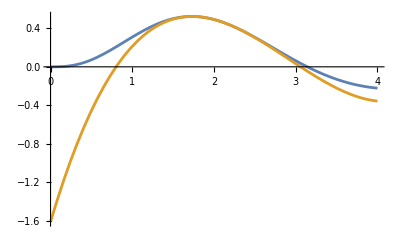

```mathematica
Plot[{f[x],taylor[x]},{x,0,4}]
```

```mathematica
Manipulate[Plot[{f[x],Evaluate[Normal[Series[f[x],{x,2,Round[n]}]]]},{x,0,4}],{n,1,10}]
```